## Metric

metric:

ds^2= -a(r)dt^2+ dr^2/(b(r))+ r^2 dθ^2+ r^2 sin^2 θ dΩ^2  .

a(r) = b(r) = 1 - (2M)/r+ζ^2/r^2(1-(2M)/r)^2  .

## Lapce function

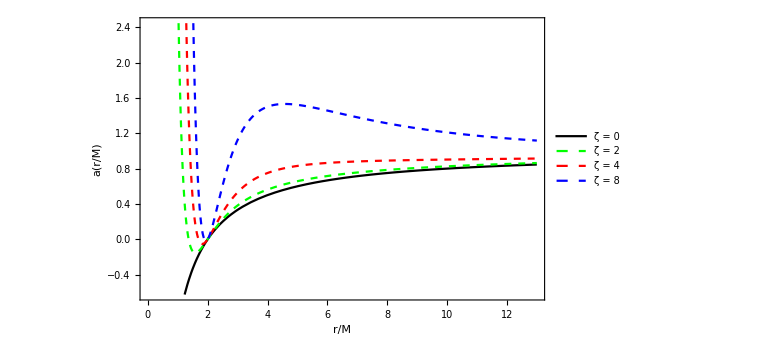

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Plot[{a[r,0],a[r,2],a[r,4],a[r,8]},{r,0,13},Frame->True,FrameLabel->{"r/M","a(r/M)"},ImageSize->Large,PlotStyle-> {{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ = 0","ζ = 2","ζ = 4","ζ = 8"},{Scaled[{0.70,0.5}],{0.8,1.45}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

### event horizon

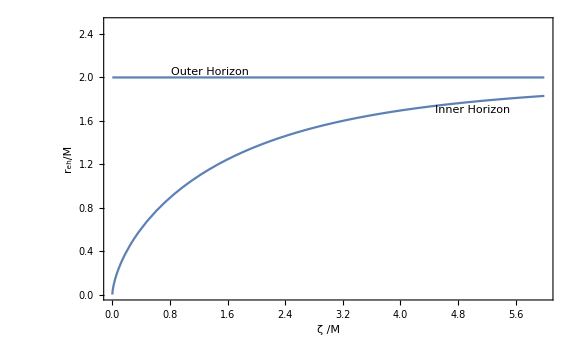

```mathematica
reh[ζ_] = r/.Solve[a[r,ζ]==0,r];
Limit[reh[ζ],ζ->Infinity];

Plot[reh[ζ],{ζ,0,6},PlotRange->{{0,6},{0,2.5}},Frame->True,FrameLabel->{"ζ /M","r_eh/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},Epilog->{Text[Rotate[Framed[Style["Outer Horizon",Italic,Bold],FrameStyle->None,Background->None],0 Degree],{1.35,2.05}],Text[Rotate[Framed[Style["Inner Horizon",Italic,Bold],FrameStyle->None,Background->None],0 Degree],{5,1.7}]},ImageSize->Large]
```

## Neutral particle motion

### effective potential

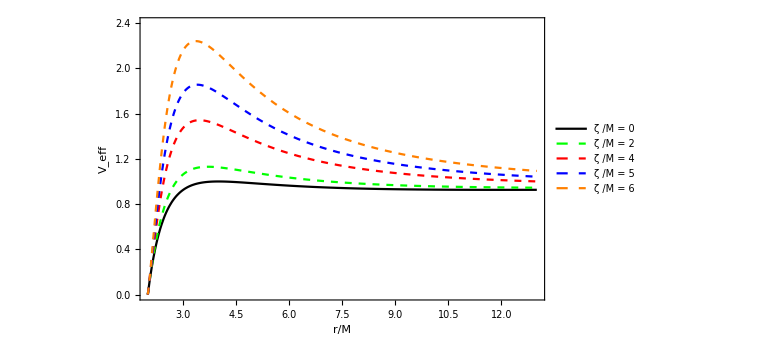

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veff[L_,r_,ζ_] := a[r,ζ](1 + L^2/r^2)
veff[Ene_,L_,ζ_,r_] :=-1 - L^2/r^2- Ene^2/a[r,ζ]
Plot[{Veff[4,r,0],Veff[4,r,2],Veff[4,r,4],Veff[4,r,5],Veff[4,r,6]},{r,2,13},PlotRange->{{2,13},{0,2.4}},Frame->True,FrameLabel->{"r/M","V_eff"," ℒ = 4"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4","ζ /M = 5","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
```

### angular momentum of particle

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 13 of {{L→-3.4641,r→6.},{L→3.4641,r→6.}} does not exist.

ReplaceAll::reps: {{{L→-3.4641,r→6.},{L→3.4641,r→6.}}⟦13⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

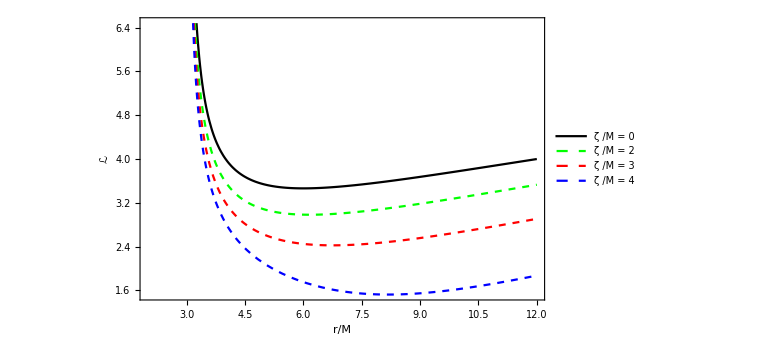

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
L[ζ_,r_]=L/.Solve[D[Veff[L,r,ζ],r]==0,L][[2]];
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
NSolve[D[L[0,r],r]==0,r];
ris[0.]//N;
Plot[{L[0,r],L[2,r],L[3,r],L[4,r]},{r,2,12},Frame->True,FrameLabel->{"r/M","ℒ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 3","ζ /M = 4"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
Plot[Ene[0,r],{r,0,5}];
(*Plot[ris[ζ],{ζ,0,4},Frame->True]*)
```

### energy of particle

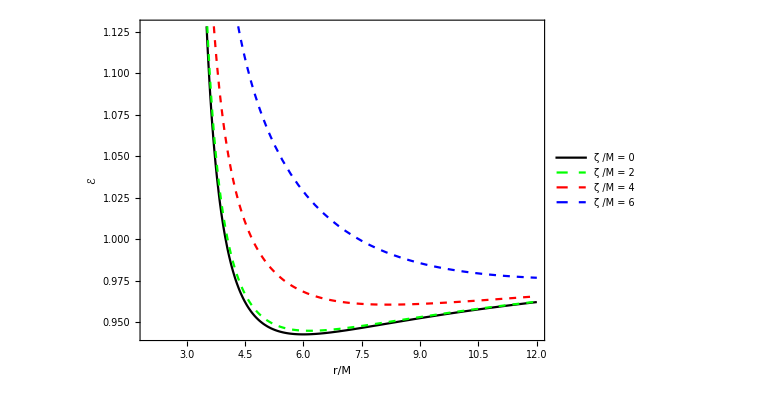

```mathematica
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
Plot[{Ene[0,r],Ene[2,r],Ene[4,r],Ene[6,r]},{r,2,12},Frame->True,FrameLabel->{"r/M","ℰ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.7]
```

### isco

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

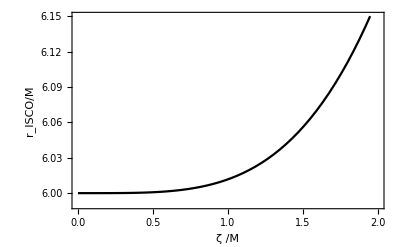

```mathematica
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
Plot[ris[ζ],{ζ,0,2},PlotRange->{{0,2},{5.99,6.15}},Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->Black]
```

## Charged particle motion

### effective potential

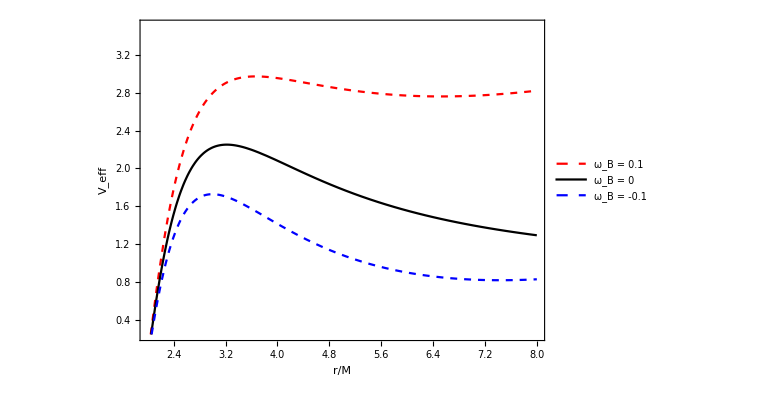

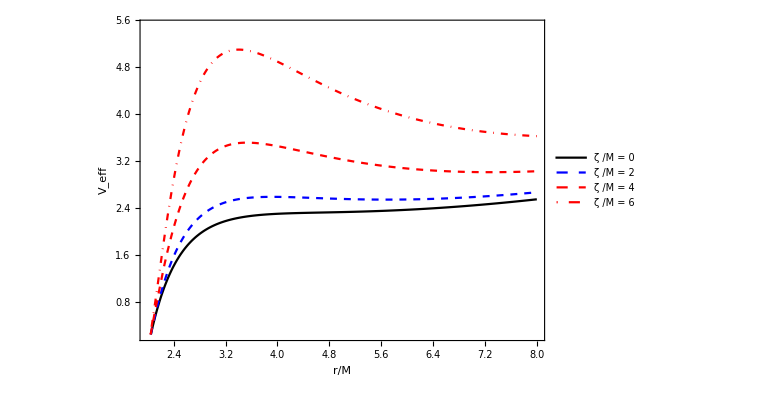

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veeff[L_,ω_,r_,ζ_] := a[r ,ζ] (1+(L/r+ ω r)^2)
Plot[{Veeff[6,0.1,r,3],Veeff[6,0,r,3],Veeff[6,-0.1,r,3]},{r,2,8},Frame->True,FrameLabel->{"r/M","V_eff"," ℒ = 6,  ζ /M = 3,   ω_B = qB/(2  mc)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Red},{Black},{Dashed, Blue}},PlotLegends->Placed[{"ω_B = 0.1", "ω_B = 0","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.7, PlotRange->{{2.,8},{0.25,3.5}}]


Plot[{Veeff[6,0.1,r,0],Veeff[6,0.1,r,2],Veeff[6,0.1,r,4],Veeff[6,0.1,r,6]},{r,2,8},Frame->True,FrameLabel->{"r/M","V_eff"," ℒ = 6, ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 0", "ζ /M = 2","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,8},{0.25,5.5}}]
```

### angular momentum

Solve::svars: Equations may not give solutions for all "solve" variables.

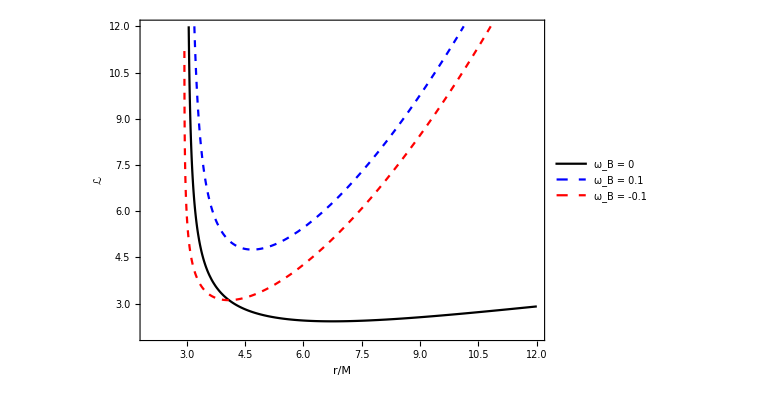

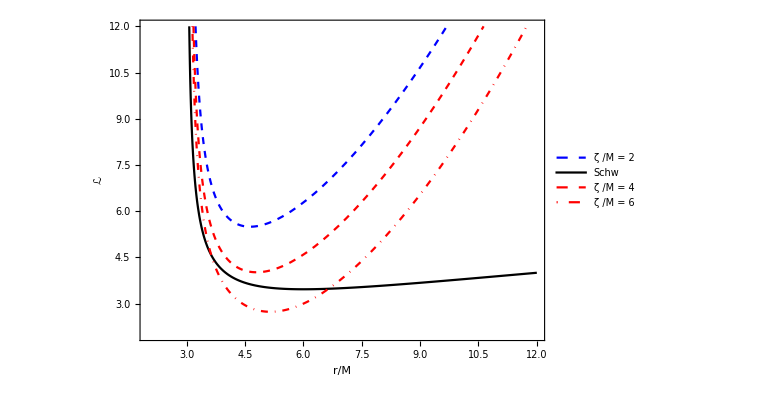

```mathematica
L[r_,ζ_,ω_] =ll/.Solve[D[a[r ,ζ] (1+(ll/r+ ω r)^2),r]==0,{ll,r}][[2]];
Solve[D[L[r,0,0],r]==0,r];
Lb[r_,ζ_,ω_]=If[L[r,3,0]<=5.91904,L[r,3,0],None];
Lr[r_,ζ_,ω_]=If[L[r,3,-0.1]<=5.93704 && r≤2.97,L[r,3,-0.1],None];
Plot[{L[r,3,0],L[r,3,0.1],L[r,3,-0.1]},{r,2,12},PlotRange->{{2,12},{2,12}},Frame->True,FrameLabel->{"r/M","ℒ","ζ /M = 3"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red}},PlotLegends->Placed[{"ω_B = 0","ω_B = 0.1","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,5},{0.25,5.5}}]


Plot[{L[r,2,0.1],L[r,0,0],L[r,4,0.1],L[r,6,0.1]},{r,2,12},PlotRange->{{2,12},{2,12}},Frame->True,FrameLabel->{"r/M","ℒ","ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Blue},{Black},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{2.2,-0.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,5},{0.25,5.5}}]
```

### energy

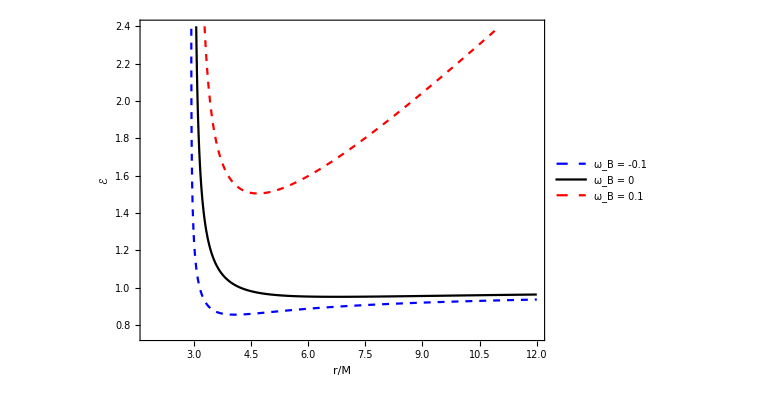

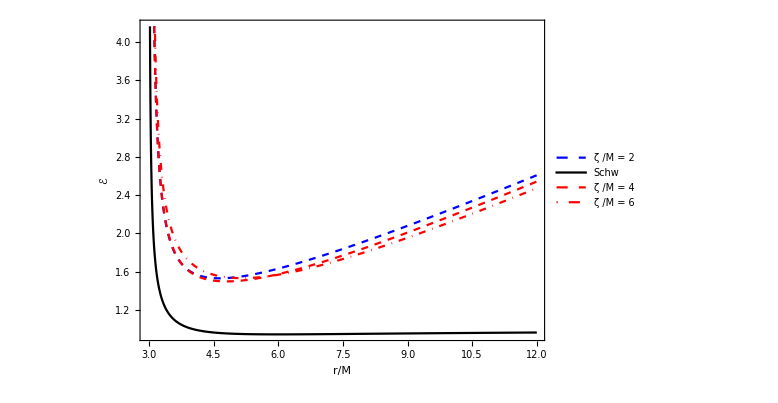

0.952579

0.958347

```mathematica
ene[r_,ζ_,ω_]:= (a[r ,ζ] (1+(L[r,ζ,ω]/r+ ω r)^2))^0.5
Plot[ene[r,3,-0.1],{r,2.95,6}];
Plot[{ene[r,3,-0.1],ene[r,3,0],ene[r,3,0.1]},{r,1.8,12},PlotRange->{{1.8,12},{0.75,2.4}},Frame->True,FrameLabel->{"r/M","ℰ","ζ /M = 3"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Blue},{Black},{Dashed,Red}},PlotLegends->Placed[{"ω_B = -0.1","ω_B = 0","ω_B = 0.1"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,Epilog->{Text[Style["●",FontFamily->"Times",9,Black],{6.746237291889099,0.9512277422287705}]}]


Plot[{ene[r,2,0.1],ene[r,0,0],ene[r,4,0.1],ene[r,6,0.1]},{r,2.97,12},Frame->True,FrameLabel->{"r/M","ℰ","ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Blue},{Black},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{2.2,-0.5}}],ImageSize->Large,AspectRatio->0.7,Epilog->{Text[Style["●",FontFamily->"Times",10,Black],{6,0.9428090415820634}]}]

ene[6,3,0.]
ene[10,3,0.]
```

### isco radii dep on ω_B

```mathematica
L1[r_,ζ_,ω_] = D[L[r,ζ,ω],r];
risc[ζ_,ω_]:=r/.FindRoot[L1[r,ζ,ω],{r,6}]
risc[4.55,0];
```

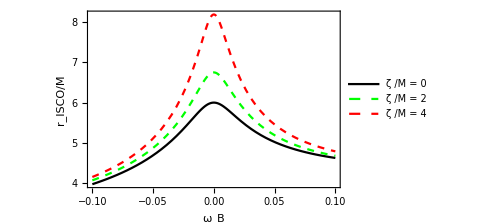

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

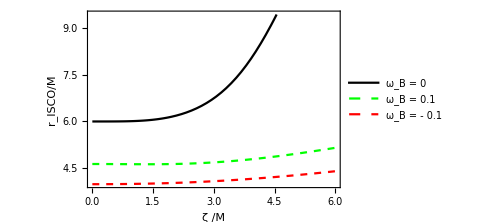

```mathematica
Plot[{risc[0,ω],risc[3,ω],risc[4,ω]},{ω,-0.1,0.1},Frame->True,FrameLabel->{"ω_B","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4"},{Scaled[{0.54,0.5}],{-0.2,-0.2}}],ImageSize->Medium]

riscB[ζ_,ω_] = If[ζ<=4.55,risc[ζ,ω],None];

Plot[{riscB[ζ,0],risc[ζ,0.1],risc[ζ,-0.1]},{ζ,0,6},Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"ω_B = 0","ω_B = 0.1","ω_B = - 0.1"},{Scaled[{0.70,0.5}],{1.5,-0.2}}],ImageSize->Medium]
```

### mimicks 𝒶 versus ω_B and ζ /M

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (1555.2-57.6 (Charting`Private`pvar$43413)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. (Charting`Private`pvar$43413)^2)^2)+(0.5 (1296.-62.4 («27»)^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. (Charting`Private`pvar$43413)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$43413,0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (1555.2-57.6 (Charting`Private`pvar$43413)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. (Charting`Private`pvar$43413)^2)^2)+(0.5 (1296.-62.4 («27»)^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. (Charting`Private`pvar$43413)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$43413,0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (-1555.2+57.6 (Charting`Private`pvar$43413)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. (Charting`Private`pvar$43413)^2)^2)+(0.5 (-1296.+62.4 («27»)^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. (Charting`Private`pvar$43413)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$43413,-0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(0.5 (540.+14. ζ^2) (1555.2-57.6 ζ^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. («1»)^2)^2)+(0.5 (1296.-62.4 ζ^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. («1»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,ζ,0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. ζ^2) (-1555.2+57.6 ζ^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. («1»)^2)^2)+(0.5 (-1296.+62.4 ζ^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. («1»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,ζ,-0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. ζ^2) (1555.2-57.6 ζ^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«2»])))/((648.+24. («1»)^2)^2)+(0.5 (1296.-62.4 ζ^2+(0.5 («1»))/(√(Power[«2»]+Times[«3»]))))/(648.+24. («1»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,ζ,0.1],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

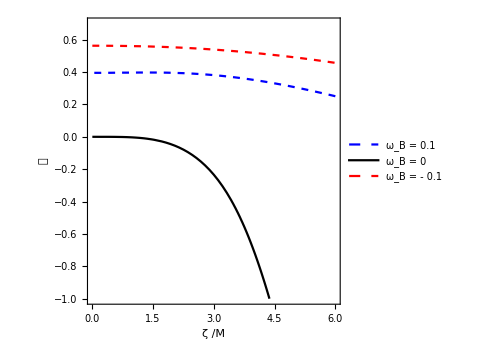

```mathematica
z1 =1+(1-Ω^2)^(1/3)((1+Ω)^(1/3)+(1-Ω)^(1/3));
z2 = Sqrt[3 Ω^2 + z1^2];
rk[Ω_]= 3+z2+If[Ω<0,1,-1] Sqrt[(3-z1)(3+z1+2 z2)]; 
l[Ω_,ζ_] = If[ζ≤4.4,rk[Ω]-risc[ζ,0.000001],None];
ContourPlot[{rk[Ω]-risc[ζ,0.1]==0,l[Ω,ζ]==0,rk[Ω]-risc[ζ,-0.1]==0},{ζ,0,6},{Ω,-1.,0.6},Frame->True,FrameLabel->{"ζ /M","𝒶"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ContourStyle->{{Dashed,Blue},{Black},{Dashed,Red}},PlotLegends->Placed[{"ω_B = 0.1","ω_B = 0","ω_B = - 0.1"},{Scaled[{0.50,0.5}],{-0.2,0.3}}],ImageSize->Medium,PlotRange->{{0,6},{-1,0.7}}]
```

FindRoot::nlnum: The function value {-0.000643004 (15552. Charting`Private`pvar$44937+√(2.41865×10^8 Power[«2»]-2592. Plus[«2»]))+0.000771605 (12960. Charting`Private`pvar$44937+(0.5 (4.03108×10^8 Power[«2»]-2592. Plus[«2»]-2160. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,0,Charting`Private`pvar$44937],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000643004 (15552. Charting`Private`pvar$44937+√(2.41865×10^8 Power[«2»]-2592. Plus[«2»]))+0.000771605 (12960. Charting`Private`pvar$44937+(0.5 (4.03108×10^8 Power[«2»]-2592. Plus[«2»]-2160. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,0,Charting`Private`pvar$44937],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000538357 (13248. Charting`Private`pvar$44937+√(1.7551×10^8 Power[«2»]-2976. Plus[«2»]))+0.000672043 (10464. Charting`Private`pvar$44937+(0.5 (2.77254×10^8 Power[«2»]-2976. Plus[«2»]-2384. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,2,Charting`Private`pvar$44937],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.000643004 (15552. ω+√(2.41865×10^8 Power[«2»]-2592. Plus[«2»]))+0.000771605 (12960. ω+(0.5 (4.03108×10^8 Power[«2»]-2592. Plus[«2»]-2160. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,0,ω],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000538357 (13248. ω+√(1.7551×10^8 Power[«2»]-2976. Plus[«2»]))+0.000672043 (10464. ω+(0.5 (2.77254×10^8 Power[«2»]-2976. Plus[«2»]-2384. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,2,ω],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000358677 (6336. ω+√(4.01449×10^7 Power[«2»]-4128. Plus[«2»]))+0.000484496 (2976. ω+(0.5 (3.77119×10^7 Power[«2»]-4128. Plus[«2»]-3056. Plus[«2»]))/(√(Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,4,ω],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

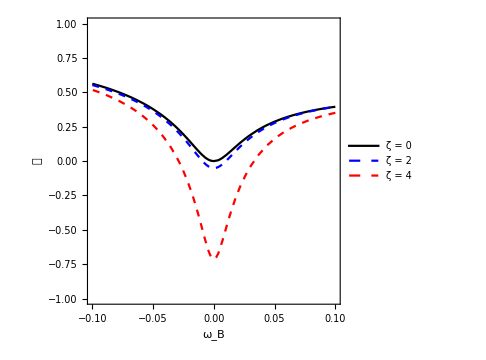

```mathematica
ContourPlot[{rk[Ω]-risc[0,ω]==0,rk[Ω]-risc[2,ω]==0,rk[Ω]-risc[4,ω]==0},{ω,-0.1,0.1},{Ω,-1,1},Frame->True,FrameLabel->{"ω_B","𝒶"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ContourStyle->{{Black},{Dashed,Blue},{Dashed,Red}},PlotLegends->Placed[{"ζ = 0","ζ = 2","ζ = 4"},{Scaled[{0.60,0.25}],{-0.2,0.2}}],ImageSize->Medium]
```

### ζ versus of ω degeneracy

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (15552. Charting`Private`pvar$12854-576. Charting`Private`pvar$12854 (Charting`Private`pvar$12855)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«4»])))/((648.+24. (Charting`Private`pvar$12855)^2)^2)+(0.5 (12960. Charting`Private`pvar$12854-«1»+(«4»«1»«1»)/(√(«1»))))/(648.+24. («27»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$12855,Charting`Private`pvar$12854],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (15552. Charting`Private`pvar$12854-576. Charting`Private`pvar$12854 (Charting`Private`pvar$12855)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«4»])))/((648.+24. (Charting`Private`pvar$12855)^2)^2)+(0.5 (12960. Charting`Private`pvar$12854-«1»+(«4»«1»«1»)/(√(«1»))))/(648.+24. («27»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$12855,Charting`Private`pvar$12854],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (15552. Charting`Private`pvar$12854-576. Charting`Private`pvar$12854 (Charting`Private`pvar$12855)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«4»])))/((648.+24. (Charting`Private`pvar$12855)^2)^2)+(0.5 (12960. Charting`Private`pvar$12854-«1»+(«4»«1»«1»)/(√(«1»))))/(648.+24. («27»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$12855,Charting`Private`pvar$12854],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

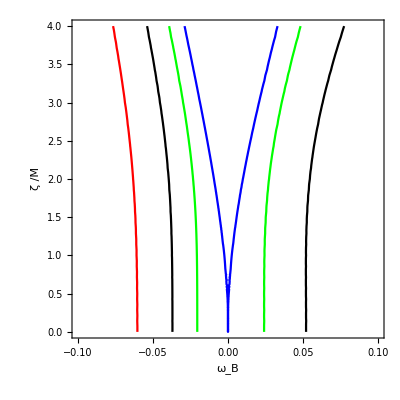

FindRoot::nlnum: The function value -FractionBox[0.5`\ (540.` + 14.`\ SuperscriptBox[«27», 2])\ (15552.`\ Charting`Private`pvar$17200 - 576.`\ Charting`Private`pvar$17200\ SuperscriptBox[Charting`Private`pvar$17201, 2] + SqrtBox[SuperscriptBox[Plus[«2»], 2] - 4.`\ Plus[«2»]\ Plus[«4»]]), SuperscriptBox[(648.` + 24.`\ SuperscriptBox[Charting`Private`pvar$17201, 2]), 2]] is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$17201,Charting`Private`pvar$17200],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (15552. Charting`Private`pvar$17200-576. Charting`Private`pvar$17200 (Charting`Private`pvar$17201)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«4»])))/((648.+24. (Charting`Private`pvar$17201)^2)^2)+(0.5 (12960. Charting`Private`pvar$17200-«1»+(«4»«1»«1»)/(√(«1»))))/(648.+24. («27»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$17201,Charting`Private`pvar$17200],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(0.5 (540.+14. («27»)^2) (15552. Charting`Private`pvar$17200-576. Charting`Private`pvar$17200 (Charting`Private`pvar$17201)^2+√(Plus[«2»]^2-4. Plus[«2»] Plus[«4»])))/((648.+24. (Charting`Private`pvar$17201)^2)^2)+(0.5 (12960. Charting`Private`pvar$17200-«1»+(«4»«1»«1»)/(√(«1»))))/(648.+24. («27»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[L1[r,Charting`Private`pvar$17201,Charting`Private`pvar$17200],{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ContourPlot[{risc[ζ,ω]==5,risc[ζ,ω]==4.5,risc[ζ,ω]==5.5,risc[ζ,ω]==6},{ω,-0.1,0.1},{ζ,0,4.},ContourStyle->{Black,Red,Green,Blue},Frame->True,FrameLabel->{"ω_B","ζ /M"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black]]
```

## Magnetic dipole motion

### effective potential

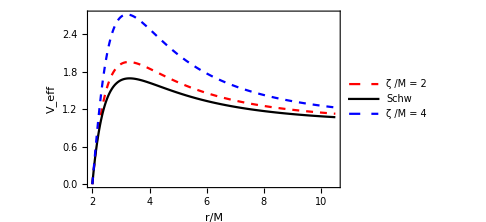

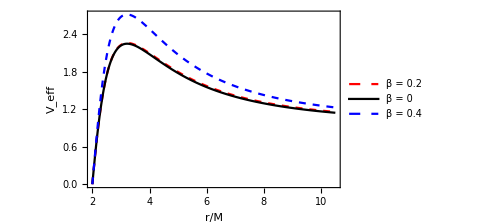

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2;
vef[r_,L_,ζ_,β_] = a[r,ζ] (L^2/r^2+a[r,ζ]^1.5/r  β + 1);
Plot[{vef[r,6,2,0.4],vef[r,6,0,0],vef[r,6,4,0.4]},{r,2,10.5},Frame->True,FrameLabel->{"r/M","V_eff","ℒ = 6, β = 0.4"},PlotStyle->{{Dashed,Red},Black,{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4"},{Scaled[{0.30,0.05}],{0.3,0.1}}],LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ImageSize->Medium]


Plot[{vef[r,6,3,0.2],vef[r,6,3,0],vef[r,6,4,0.4]},{r,2,10.5},Frame->True,FrameLabel->{"r/M","V_eff","ℒ = 6, ζ /M = 3"},PlotStyle->{{Dashed,Red},Black,{Dashed,Blue}},PlotLegends->Placed[{"β = 0.2","β = 0","β = 0.4"},{Scaled[{0.30,0.1}],{0.3,0.1}}],LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ImageSize->Medium]
```

### angular momentum

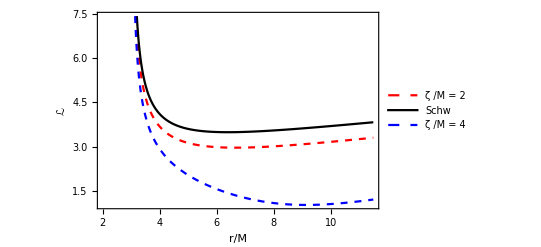

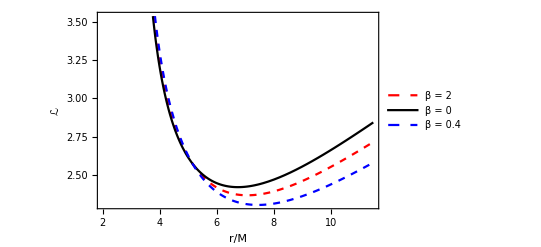

```mathematica
L[r_,ζ_,β_] = L/.Solve[D[vef[r,L,ζ,β],r]==0,L][[2]];
Plot[{L[r,2,0.4],L[r,0,0.4],L[r,4,0.4]},{r,2,11.5},Frame->True,FrameLabel->
{"r/M","ℒ","β = 0.4"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Red},Black,{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4"},{Scaled[{0.70,0.5}],{0.3,0.1}}]]


Plot[{L[r,3,0.2],L[r,3,0],L[r,3,0.4]},{r,2,11.5},Frame->True,FrameLabel->
{"r/M","ℒ","ζ /M = 3"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Red},Black,{Dashed,Blue}},PlotLegends->Placed[{"β = 2","β = 0","β = 0.4"},{Scaled[{0.70,0.5}],{0.3,0.1}}]]
```

```mathematica
ll[r_,ζ_,β_] = D[L[r,ζ,β],r]//Simplify;
```

### isco radii of β, ζ

```mathematica
ris[ζ_,β_]=r/.FindRoot[ll[r,ζ,β]==0,{r,6}];
z1 =1+(1-Ω^2)^(1/3)((1+Ω)^(1/3)+(1-Ω)^(1/3));
z2 = Sqrt[3 Ω^2 + z1^2];
rk[Ω_]= 3+z2-Sqrt[(3-z1)(3+z1+2 z2)]; 
ris[0,0]
```

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 ζ^2)^0.5 √(«1») «1» √(3.35923×10^6-124416. ζ^2+«1»-«1»-«1»-559872. β («1»)^1.5-41472. β ζ^2 (0.666667+Times[«2»])^1.5))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 ζ^2)^0.5 √(«1») «1» √(3.35923×10^6-124416. ζ^2+«1»-«1»-«1»-559872. β («1»)^1.5-41472. β ζ^2 (0.666667+Times[«2»])^1.5))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

6.

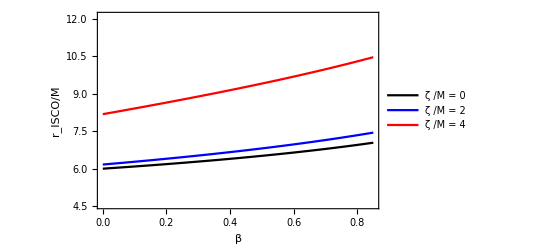

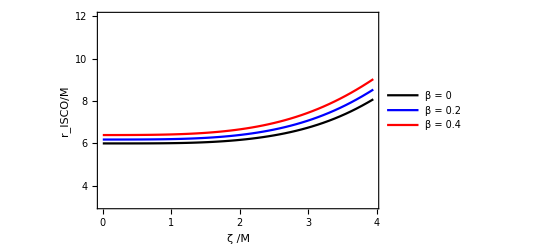

```mathematica
Plot[{ris[0,β],ris[2,β],ris[4,β],(*rk[β]*)},{β,0,0.85},PlotStyle->{Black,Blue,Red,Dotted},PlotRange->{{0,0.85},{4.55,12.1}},Frame->True,FrameLabel->{"β","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],PlotStyle->{Black,{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 0", "ζ /M = 2","ζ /M = 4"(*,"𝒦ℯ𝓇𝓇"*)},{Scaled[{0.58,0.6}],{1.7,0.1}}]]


Plot[{ris[ζ,0],ris[ζ,0.2],ris[ζ,0.4](*,rk[ζ]*)},{ζ,0,3.95},PlotStyle->{Black,Blue,Red,Dotted},PlotRange->{{0,3.95},{3.1,12}},Frame->True,Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],PlotStyle->{Black,{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"β = 0", "β = 0.2","β = 0.4"(*,"𝒦ℯ𝓇𝓇"*)},{Scaled[{0.6,0.5}],{1.7,0.1}}]]
```

```mathematica
ris[0,0]
```

6.

### degeneracy ζ versus of β

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 (Charting`Private`pvar$55630)^2) (648.+24. («27»)^2) √(«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$55630,Charting`Private`pvar$55629]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 (Charting`Private`pvar$55630)^2) (648.+24. («27»)^2) √(«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$55630,Charting`Private`pvar$55629]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 (Charting`Private`pvar$55630)^2) (648.+24. («27»)^2) √(«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$55630,Charting`Private`pvar$55629]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 ζ^2)^0.5 √(«1») «1» √(3.35923×10^6-124416. ζ^2+«1»-«1»-«1»-559872. β («1»)^1.5-41472. β ζ^2 (0.666667+Times[«2»])^1.5))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 ζ^2)^0.5 √(«1») «1» √(3.35923×10^6-124416. ζ^2+«1»-«1»-«1»-559872. β («1»)^1.5-41472. β ζ^2 (0.666667+Times[«2»])^1.5))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (0.+«22»))/((0.666667+0.0123457 ζ^2)^0.5 √(«1») «1» √(3.35923×10^6-124416. ζ^2+«1»-«1»-«1»-559872. β («1»)^1.5-41472. β ζ^2 (0.666667+Times[«2»])^1.5))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,ζ,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

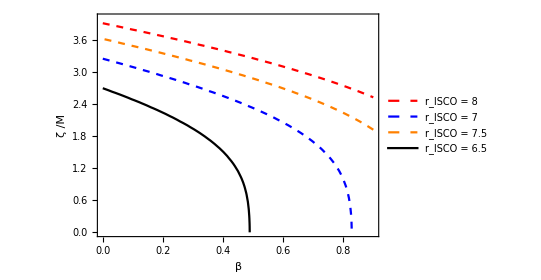

```mathematica
ContourPlot[{ris[ζ,β]==8,ris[ζ,β]==7,ris[ζ,β]==7.5,ris[ζ,β]==6.5},{β,0,0.9},{ζ,0,4.},Frame->True,FrameLabel->{"β","ζ /M"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ContourStyle->{{Red,Dashed},{Blue,Dashed},{Orange,Dashed},Black},AspectRatio->0.7,PlotLegends->Placed[{"r_ISCO = 8", "r_ISCO = 7","r_ISCO = 7.5","r_ISCO = 6.5"},{Scaled[{0.7,0.05}],{1.7,0.1}}]]
```

### mimicks 𝒶 versus of ζ and β {spin of ζ, β}

FindRoot::nlnum: The function value {(4.59394×10^-10 (0.000488281-3.26517×10^11 Charting`Private`pvar$57261))/(√(3.35923×10^6+152378. Charting`Private`pvar$57261))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,0,Charting`Private`pvar$57261]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(4.59394×10^-10 (0.000488281-3.26517×10^11 Charting`Private`pvar$57261))/(√(3.35923×10^6+152378. Charting`Private`pvar$57261))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,0,Charting`Private`pvar$57261]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(3.60306×10^-10 (-7.85914×10^10-4.91531×10^11 Charting`Private`pvar$57261))/(√(2.86157×10^6-6282.17 Charting`Private`pvar$57261))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,2,Charting`Private`pvar$57261]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {(4.59394×10^-10 (0.000488281-3.26517×10^11 β))/(√(3.35923×10^6+152378. β))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,0,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(3.60306×10^-10 (-7.85914×10^10-4.91531×10^11 β))/(√(2.86157×10^6-6282.17 β))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,2,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.00759×10^-10 (-1.38143×10^12-1.36951×10^12 β))/(√(1.36858×10^6-708000. β))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,4,β]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

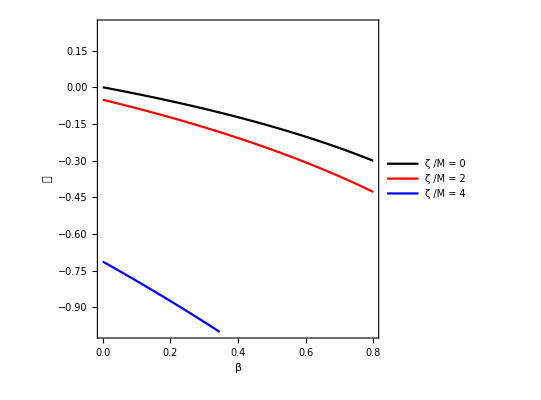

```mathematica
z1 =1+(1-Ω^2)^(1/3)((1+Ω)^(1/3)+(1-Ω)^(1/3));
z2 = Sqrt[3 Ω^2 + z1^2];
rk[Ω_]= 3+z2+If[Ω>0,-1,1]Sqrt[(3-z1)(3+z1+2 z2)]; 
ContourPlot[{rk[x]-ris[0,β]==0,rk[x]-ris[2,β]==0,rk[x]-ris[4,β]==0},{β,0,0.8},{x,-1,0.5},ContourStyle->{Black,Red,Blue},Frame->True,FrameLabel->{"β","𝒶"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ContourStyle->{{Black},{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{"ζ /M = 0", "ζ /M = 2","ζ /M = 4"},{Scaled[{0.7,0.2}],{1.7,0.1}}],PlotRange->{{0,0.8},{-1,0.25}}]
```

FindRoot::nlnum: The function value {(2.4306×10^-7 («1»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 («27»)^2) (648.+24. («27»)^2) √(3.35923×10^6-124416. («27»)^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$58473,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 («1»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 («27»)^2) (648.+24. («27»)^2) √(3.35923×10^6-124416. («27»)^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$58473,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 («1»))/((0.666667+0.0123457 («27»)^2)^0.5 √(1.+0.037037 («27»)^2) (648.+24. («27»)^2) √(3.35923×10^6-124416. («27»)^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,Charting`Private`pvar$58473,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {(2.4306×10^-7 (1.56728×10^10-2.90238×10^8 ζ^2-«22» ζ^4+«17»))/((0.666667+0.0123457 ζ^2)^0.5 √(1.+0.037037 ζ^2) (648.+24. ζ^2) √(3.35923×10^6-124416. ζ^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (1.56728×10^10-2.90238×10^8 ζ^2-«22» ζ^4+«17»))/((0.666667+0.0123457 ζ^2)^0.5 √(1.+0.037037 ζ^2) (648.+24. ζ^2) √(3.35923×10^6-124416. ζ^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[ll[r,ζ,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2.4306×10^-7 (1.56728×10^10-2.90238×10^8 ζ^2-«22» ζ^4+«17»))/((0.666667+0.0123457 ζ^2)^0.5 √(1.+0.037037 ζ^2) (648.+24. ζ^2) √(3.35923×10^6-124416. ζ^2+«9»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ll[r,ζ,0.4]==0,{r,6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

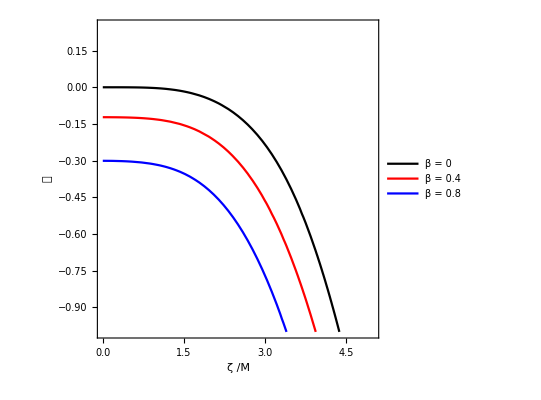

```mathematica
Clear[y,t]
y[x_,ζ_] = If[ζ≤4,rk[x]-ris[ζ,0.8],None];
t[x_,ζ_] = If[ζ≤4.5,rk[x]-ris[ζ,0],None];
ContourPlot[{t[x,ζ]==0,rk[x]-ris[ζ,0.4]==0,y[x,ζ]==0},{ζ,0,5},{x,-1,0.5},ContourStyle->{Black,Red,Blue},Frame->True,FrameLabel->{"ζ /M","𝒶"},LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ContourStyle->{{Black},{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{"β = 0", "β = 0.4","β = 0.8"},{Scaled[{0.7,0.1}],{1.7,0.1}}],PlotRange->{{0,5},{-1,0.25}}]
```